```mathematica
f1 = a*Exp[-t/t0]*HeavisideTheta[t]
```

a ⅇ^(-t/t0) HeavisideTheta[t]

```mathematica
f2 = UnitBox[-(t-1/(2*fs))*fs]
```

UnitBox[fs (1/(2 fs)-t)]

```mathematica
UnitBox[fs (-1/(2*fs)+t)]
```

UnitBox[fs (-1/(2 fs)+t)]

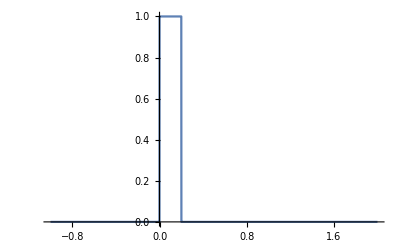

```mathematica
Plot[f2 /. fs -> 5, {t,-1,2}]
```

```mathematica
g = Convolve[f1,f2,t,tt]
```

a (Piecewise[{{t0, fs==0}, {-ⅇ^(-tt/t0) t0 (ⅇ^(1/(fs t0))-ⅇ^(tt/t0)-HeavisideTheta[tt]+ⅇ^(tt/t0) HeavisideTheta[tt]) HeavisideTheta[-1/fs+tt], fs<0}, {-ⅇ^(-tt/t0) t0 HeavisideTheta[tt] (1-ⅇ^(tt/t0)-ⅇ^(1/(fs t0)) HeavisideTheta[-1/fs+tt]+ⅇ^(tt/t0) HeavisideTheta[-1/fs+tt]), True}}])

```mathematica
gg= Simplify[g]
```

a (Piecewise[{{t0, fs==0}, {-ⅇ^(-tt/t0) t0 (ⅇ^(1/(fs t0))-ⅇ^(tt/t0)+(-1+ⅇ^(tt/t0)) HeavisideTheta[tt]) HeavisideTheta[-1/fs+tt], fs<0}, {-ⅇ^(-tt/t0) t0 HeavisideTheta[tt] (1-ⅇ^(tt/t0)+(-ⅇ^(1/(fs t0))+ⅇ^(tt/t0)) HeavisideTheta[-1/fs+tt]), True}}])

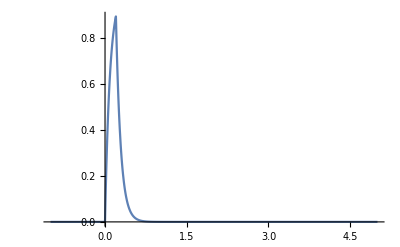

```mathematica
Plot[gg /. {fs -> 5,t0 -> 0.089,a -> 1/0.089},{tt,-1,5}, PlotRange -> All]
```

```mathematica
Integrate[f,t]
```

f t

```mathematica
func = a*t0*(1-Exp[-tt/t0])*HeavisideTheta[1/fs - tt]*HeavisideTheta[tt] +a*t0*Exp[-tt/t0]*(Exp[1/(fs*t0)] - 1)*HeavisideTheta[tt - 1/fs]
```

a (1-ⅇ^(-tt/t0)) t0 HeavisideTheta[1/fs-tt] HeavisideTheta[tt]+a ⅇ^(-tt/t0) (-1+ⅇ^(1/(fs t0))) t0 HeavisideTheta[-1/fs+tt]

```mathematica
Plot[{func  /. {t0 -> 0.089, fs -> 5, a -> 1/0.089}},{tt,-1,5},PlotRange->All]
```

-Graphics-

```mathematica
func - gg /. {t0 -> 0.089, fs -> 5, a -> 1/0.089, tt -> 2}
```

-3.89334×10^-17

11.236

```mathematica
{{□}, {□}}
```